### Settings

```mathematica
dx = 0.458;
dy = 0.648;
a=10;
delta =0.0001;
rMax=10; 
Z =0.8; 
m = 0.152;
coord = {{-5*dx,0},{5*dx,0},{0,-4*dy},{0,4*dy},{4*dx, 3*dy},{4*dx, -3*dy},{-4*dx, 3*dy},{-4*dx, -3*dy}};
```

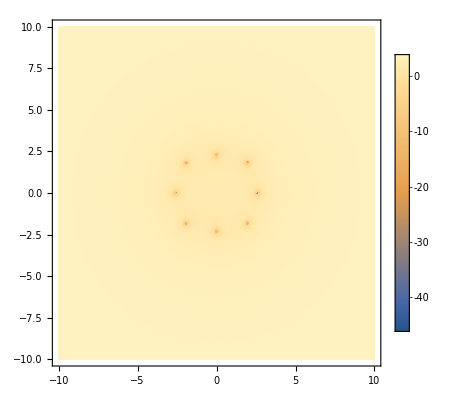

```mathematica
V[r_, θ_] := Sum[(-Z)/(Sqrt[(r*Sin[θ]- coord[[i]][[1]])^2  + (r*Cos[θ]-coord[[i]][[2]])^2]+delta)*Exp[-Sqrt[(r*Sin[θ]-coord[[i]][[1]])^2  + (r*Cos[θ]-coord[[i]][[2]])^2]/a],{i,8} ] +4;
DensityPlot[V[r ,θ]/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-rMax,rMax},{y,-rMax,rMax}, (*PlotTheme->"Minimal",*) PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
(*Export[NotebookDirectory[]<>"Coulomb.png",%,ImageResolution->100];*)
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/(2*m))* Laplacian[R2D[r,θ],{r,θ},"Polar"]+V[r,θ]*R2D[r,θ],
DirichletCondition[R2D[r,θ]==0,r==rMax*Sqrt[2]&&0<θ<=2*Pi],
PeriodicBoundaryCondition[R2D[r,θ],θ==0,TranslationTransform[{0,2 π}]]},
R2D[r,θ],{r,0,rMax*Sqrt[2]},{θ,0,2 π},8, Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->1000000}(* "Direct"*),"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}  ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

{2.13953,2.96468,3.02229,3.79367,3.84465,3.87426,4.01958,4.0256}

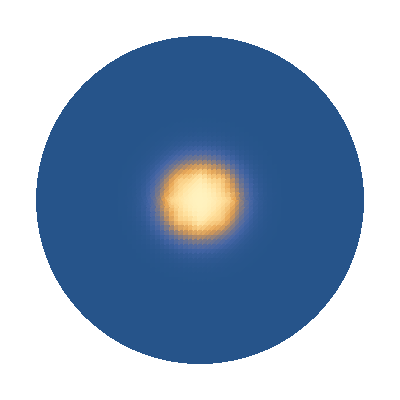

```mathematica
F1 =Part[Re[egnVec],Part[ord,1]]^2;
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All];
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y]+2π,{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal", PlotPoints->100,PlotRange->All  (*PlotLegends->Automatic*)];
Show[{%,%%}]
Export[NotebookDirectory[]<>"1.png",%,ImageResolution->100];
```

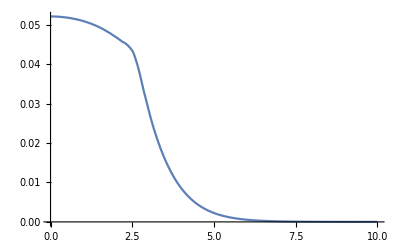

```mathematica
Plot[F1/.r->x/.θ->0, {x, 0, rMax },PlotRange->All]
Export[NotebookDirectory[]<>"1_line.png",%,ImageResolution->100];
```